## Aplicación de Listas (Arreglos, Matrices)

```mathematica
image = Import["http://mahtblog.files.wordpress.com/2011/03/imagen2013.png?w=788"]
```

-Graphics-

```mathematica
image//ImageDimensions
```

{500,375}

```mathematica
image01 = image//ImageData;
```

```mathematica
image01//Dimensions
```

{375,500,3}

```mathematica
image01[[1]]//MatrixForm;
```

```mathematica
Image[{image01[[1]],image01[[2]]}]
```

-Graphics-

```mathematica
Image[
Table[image01[[i]], {i, 1, 375}]
]
```

-Graphics-

```mathematica
Manipulate[Image[
Table[image01[[i]], {i, 1, j}]
], {j, 1,375}]
```

Part::partd: Part specification image01 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification image01 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification image01 ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Image::imgarray: The specified argument {image01 ⟦ 1 ⟧, image01 ⟦ 2 ⟧, image01 ⟦ 3 ⟧, image01 ⟦ 4 ⟧, image01 ⟦ 5 ⟧, image01 ⟦ 6 ⟧, image01 ⟦ 7 ⟧, image01 ⟦ 8 ⟧, image01 ⟦ 9 ⟧, image01 ⟦ 10 ⟧, image01 ⟦ 11 ⟧, image01 ⟦ 12 ⟧, image01 ⟦ 13 ⟧, image01 ⟦ 14 ⟧, image01 ⟦ 15 ⟧, image01 ⟦ 16 ⟧, « 19 », image01 ⟦ 36 ⟧, image01 ⟦ 37 ⟧, image01 ⟦ 38 ⟧, image01 ⟦ 39 ⟧, image01 ⟦ 40 ⟧, image01 ⟦ 41 ⟧, image01 ⟦ 42 ⟧, image01 ⟦ 43 ⟧, image01 ⟦ 44 ⟧, image01 ⟦ 45 ⟧, image01 ⟦ 46 ⟧, image01 ⟦ 47 ⟧, image01 ⟦ 48 ⟧, image01 ⟦ 49 ⟧, image01 ⟦ 50 ⟧, « 90 »} should be an array of rank 2 or 3 with machine-sized numbers.

```mathematica
image01[[1]][[1]]
```

{0.129412,0.141176,0.0705882}

```mathematica
image01[[1]][[1, 1]]
```

0.129412

```mathematica
matrix =Table[{image01[[i]][[j, 3]], image01[[i]][[j, 2]], image01[[i]][[j, 1]]}, {i, 1, 375}, {j, 1, 500}];
```

```mathematica
matrix[[1]]//MatrixForm;
```

```mathematica
Table[{image01[[i]][[j, 3]], image01[[i]][[j, 2]], image01[[i]][[j, 1]]}, {i, 1, 375}, {j, 1, 500}]//Dimensions
```

{375,500,3}

```mathematica
(** Fisrt Attempt **)
Image[
Table[{image01[[i]][[j, 3]], image01[[i]][[j, 2]], image01[[i]][[j, 1]]}, {i, 1, 375}, {j, 1, 500}]
](** Success! **)
```

-Graphics-

```mathematica
Image[
Table[{image01[[i]][[j, 2]], image01[[i]][[j, 3]], image01[[i]][[j, 1]]}, {i, 1, 375}, {j, 1, 500}]
]
```

-Graphics-

```mathematica
Image[
Table[{image01[[i]][[j, 3]], image01[[i]][[j, 1]], image01[[i]][[j, 2]]}, {i, 1, 375}, {j, 1, 500}]
]
```

-Graphics-

```mathematica
Image[
Table[{image01[[i]][[j, 3]], image01[[i]][[j, 3]], image01[[i]][[j, 3]]}, {i, 1, 375}, {j, 1, 500}]
]
```

-Graphics-

## Excel y Listas

```mathematica
data = Import["C:\\Users\\FatalRaincloud\\Downloads\\datos2009.xls"][[1]];
```

```mathematica
data//Dimensions
```

{25,3}

```mathematica
data
```

{{Fecha ,número día,Horas de luz},{{2009,1,1,0,0,0.},1.,11.},{{2009,1,16,0,0,0.},16.,11.116},{{2009,2,1,0,0,0.},32.,11.316},{{2009,2,16,0,0,0.},47.,11.55},{{2009,3,1,0,0,0.},60.,11.766},{{2009,3,16,0,0,0.},75.,12.05},{{2009,4,1,0,0,0.},91.,12.333},{{2009,4,16,0,0,0.},106.,12.6},{{2009,5,1,0,0,0.},121.,12.85},{{2009,5,16,0,0,0.},136.,13.066},{{2009,6,1,0,0,0.},152.,13.216},{{2009,6,16,0,0,0.},167.,13.3},{{2009,7,1,0,0,0.},182.,13.266},{{2009,7,16,0,0,0.},197.,13.166},{{2009,8,1,0,0,0.},213.,12.983},{{2009,8,16,0,0,0.},228.,12.766},{{2009,9,1,0,0,0.},244.,12.5},{{2009,9,16,0,0,0.},259.,12.233},{{2009,10,1,0,0,0.},274.,11.95},{{2009,10,16,0,0,0.},289.,11.683},{{2009,11,1,0,0,0.},305.,11.416},{{2009,11,16,0,0,0.},320.,11.216},{{2009,12,1,0,0,0.},335.,11.05},{{2009,12,16,0,0,0.},350.,10.983}}

```mathematica
Grid[data, Frame-> All, ItemSize->Automatic, Background->{None, {{LightPurple, LightBlue}}}]
```

Fecha  | número día | Horas de luz
{2009,1,1,0,0,0.} | 1. | 11.
{2009,1,16,0,0,0.} | 16. | 11.116
{2009,2,1,0,0,0.} | 32. | 11.316
{2009,2,16,0,0,0.} | 47. | 11.55
{2009,3,1,0,0,0.} | 60. | 11.766
{2009,3,16,0,0,0.} | 75. | 12.05
{2009,4,1,0,0,0.} | 91. | 12.333
{2009,4,16,0,0,0.} | 106. | 12.6
{2009,5,1,0,0,0.} | 121. | 12.85
{2009,5,16,0,0,0.} | 136. | 13.066
{2009,6,1,0,0,0.} | 152. | 13.216
{2009,6,16,0,0,0.} | 167. | 13.3
{2009,7,1,0,0,0.} | 182. | 13.266
{2009,7,16,0,0,0.} | 197. | 13.166
{2009,8,1,0,0,0.} | 213. | 12.983
{2009,8,16,0,0,0.} | 228. | 12.766
{2009,9,1,0,0,0.} | 244. | 12.5
{2009,9,16,0,0,0.} | 259. | 12.233
{2009,10,1,0,0,0.} | 274. | 11.95
{2009,10,16,0,0,0.} | 289. | 11.683
{2009,11,1,0,0,0.} | 305. | 11.416
{2009,11,16,0,0,0.} | 320. | 11.216
{2009,12,1,0,0,0.} | 335. | 11.05
{2009,12,16,0,0,0.} | 350. | 10.983

```mathematica
data01=data[[2;;25, {2, 3}]];
```

```mathematica
Grid[data01, Frame-> All, ItemSize->Automatic, Background->{None, {{LightPurple, LightBlue}}}]
```

1. | 11.
16. | 11.116
32. | 11.316
47. | 11.55
60. | 11.766
75. | 12.05
91. | 12.333
106. | 12.6
121. | 12.85
136. | 13.066
152. | 13.216
167. | 13.3
182. | 13.266
197. | 13.166
213. | 12.983
228. | 12.766
244. | 12.5
259. | 12.233
274. | 11.95
289. | 11.683
305. | 11.416
320. | 11.216
335. | 11.05
350. | 10.983

```mathematica
datos02 = data[[{1, 2, 5, 7}, {2, 3}]];
```

```mathematica
Grid[datos02, Frame-> All, ItemSize->Automatic, Background->{None, {{LightGray, LightOrange}}}]
```

número día | Horas de luz
1. | 11.
47. | 11.55
75. | 12.05

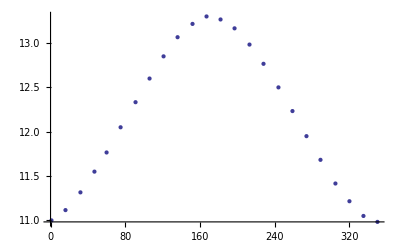

```mathematica
ListPlot[data01]
```

```mathematica
Clear[a,b,c,d];
```

```mathematica
modelo = a*Sin[b*x Pi/180 +c] + d;
```

```mathematica
regresion = FindFit[data01, modelo, {a,b,c,d},x]
```

{a→-1.14502,b→0.967441,c→1.80909,d→12.1205}

```mathematica
regreF = Function[{}, Evaluate[modelo/.regresion]];
```

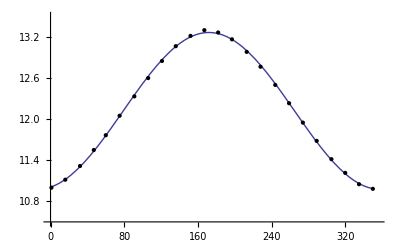

```mathematica
Plot[regreF[x], {x, 1, 350}, PlotRange->{{0, 355}, {10.5, 13.5}}, Epilog->Map[Point, data01]]
(** Epilog; brings discrethe data into continous data **)
```

```mathematica
modelo01 = a*x^2+b*x+c;
```

```mathematica
regresion = FindFit[data01, modelo01, {a,b,c,d},x]
```

{a→-0.0000784499,b→0.027182,c→10.6558,d→0.}

```mathematica
regreF = Function[{}, Evaluate[modelo01/.regresion]];
```

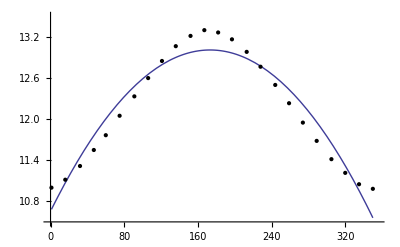

```mathematica
Plot[regreF[x], {x, 1, 350}, PlotRange->{{0, 355}, {10.5, 13.5}}, Epilog->Map[Point, data01]]
(** Epilog; brings discrethe data into continous data **)
```

## Generación de Imagen Vertical

```mathematica
Image[
Table[image01[[i]][[j]], {i, 1, 375}, {j, 1, 250}]
]
```

-Graphics-

```mathematica
Manipulate[Image[
	Table[image01[[i]][[j]], {i, 1, 375}, {j, 1, k}]
	], {k, 1, 500}
]
```

Part::partd: Part specification image01 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 3 of image01 ⟦ 1 ⟧ does not exist.

Part::partw: Part 4 of image01 ⟦ 1 ⟧ does not exist.

Part::partw: Part 5 of image01 ⟦ 1 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Image::imgarray: The specified argument {{image01, 1, image01 ⟦ 1 ⟧ ⟦ 3 ⟧, image01 ⟦ 1 ⟧ ⟦ 4 ⟧, image01 ⟦ 1 ⟧ ⟦ 5 ⟧, image01 ⟦ 1 ⟧ ⟦ 6 ⟧, image01 ⟦ 1 ⟧ ⟦ 7 ⟧, image01 ⟦ 1 ⟧ ⟦ 8 ⟧, image01 ⟦ 1 ⟧ ⟦ 9 ⟧, image01 ⟦ 1 ⟧ ⟦ 10 ⟧, « 31 », image01 ⟦ 1 ⟧ ⟦ 42 ⟧, image01 ⟦ 1 ⟧ ⟦ 43 ⟧, image01 ⟦ 1 ⟧ ⟦ 44 ⟧, image01 ⟦ 1 ⟧ ⟦ 45 ⟧, image01 ⟦ 1 ⟧ ⟦ 46 ⟧, image01 ⟦ 1 ⟧ ⟦ 47 ⟧, image01 ⟦ 1 ⟧ ⟦ 48 ⟧, image01 ⟦ 1 ⟧ ⟦ 49 ⟧, image01 ⟦ 1 ⟧ ⟦ 50 ⟧, « 450 »}, « 49 », « 325 »} should be an array of rank 2 or 3 with machine-sized numbers.

Part::partd: Part specification image01 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 3 of image01 ⟦ 1 ⟧ does not exist.

Part::partw: Part 4 of image01 ⟦ 1 ⟧ does not exist.

Part::partw: Part 5 of image01 ⟦ 1 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Image::imgarray: The specified argument {« 1 »} should be an array of rank 2 or 3 with machine-sized numbers.

Part::partd: Part specification image01 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 3 of image01 ⟦ 1 ⟧ does not exist.

Part::partw: Part 4 of image01 ⟦ 1 ⟧ does not exist.

Part::partw: Part 5 of image01 ⟦ 1 ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Image::imgarray: The specified argument {{image01, 1, image01 ⟦ 1 ⟧ ⟦ 3 ⟧, image01 ⟦ 1 ⟧ ⟦ 4 ⟧, image01 ⟦ 1 ⟧ ⟦ 5 ⟧, image01 ⟦ 1 ⟧ ⟦ 6 ⟧, image01 ⟦ 1 ⟧ ⟦ 7 ⟧, image01 ⟦ 1 ⟧ ⟦ 8 ⟧, image01 ⟦ 1 ⟧ ⟦ 9 ⟧, image01 ⟦ 1 ⟧ ⟦ 10 ⟧, image01 ⟦ 1 ⟧ ⟦ 11 ⟧, image01 ⟦ 1 ⟧ ⟦ 12 ⟧, image01 ⟦ 1 ⟧ ⟦ 13 ⟧, « 25 », image01 ⟦ 1 ⟧ ⟦ 39 ⟧, image01 ⟦ 1 ⟧ ⟦ 40 ⟧, image01 ⟦ 1 ⟧ ⟦ 41 ⟧, image01 ⟦ 1 ⟧ ⟦ 42 ⟧, image01 ⟦ 1 ⟧ ⟦ 43 ⟧, image01 ⟦ 1 ⟧ ⟦ 44 ⟧, image01 ⟦ 1 ⟧ ⟦ 45 ⟧, image01 ⟦ 1 ⟧ ⟦ 46 ⟧, image01 ⟦ 1 ⟧ ⟦ 47 ⟧, image01 ⟦ 1 ⟧ ⟦ 48 ⟧, image01 ⟦ 1 ⟧ ⟦ 49 ⟧, image01 ⟦ 1 ⟧ ⟦ 50 ⟧, « 450 »}, « 49 », « 325 »} should be an array of rank 2 or 3 with machine-sized numbers.

## Errores

### Observación

```mathematica
x^2+2/.x->a+h
```

2+(a+h)^2

```mathematica
regreF[100]
```

12.1205-1.14502 Sin[1.80909+0.016885 x]

```mathematica
regreF
```

Function[{},12.1205-1.14502 Sin[1.80909+0.016885 x]]

```mathematica
regreF[[2]]
```

12.1205-1.14502 Sin[1.80909+0.016885 x]

```mathematica
pronostico[y_]:=regreF[[2]]/.x->y;
```

```mathematica
pronostico[100]
```

12.5196

```mathematica
datosreales = Table[data01[[i, 2]], {i, 1, Length[data01]}]
```

{11.,11.116,11.316,11.55,11.766,12.05,12.333,12.6,12.85,13.066,13.216,13.3,13.266,13.166,12.983,12.766,12.5,12.233,11.95,11.683,11.416,11.216,11.05,10.983}

```mathematica
datospronostico = Table[pronostico[data01[[i, 1]]], {i, 1, Length[data01]}];
```

```mathematica
TableForm[Table[{i, datosreales[[i]], datospronostico[[i]], Abs[(datosreales[[i]]-datospronostico[[i]])/datosreales[[i]]*100]}, {i, 1, Length[data01]}], TableHeadings->{None, {"i", "Datos Reales", "Datos Pronóstico","Error Porcentual"}}]
```

i | Datos Reales | Datos Pronóstico | Error Porcentual
1 | 11. | 11.0126 | 0.114482
2 | 11.116 | 11.1204 | 0.0392532
3 | 11.316 | 11.3054 | 0.093566
4 | 11.55 | 11.5329 | 0.14791
5 | 11.766 | 11.761 | 0.0424567
6 | 12.05 | 12.0449 | 0.0424991
7 | 12.333 | 12.3525 | 0.15848
8 | 12.6 | 12.6261 | 0.207196
9 | 12.85 | 12.8674 | 0.135482
10 | 13.066 | 13.0611 | 0.0378314
11 | 13.216 | 13.2012 | 0.111716
12 | 13.3 | 13.2616 | 0.288974
13 | 13.266 | 13.2491 | 0.127452
14 | 13.166 | 13.1646 | 0.0105647
15 | 12.983 | 13.0013 | 0.140792
16 | 12.766 | 12.7898 | 0.186729
17 | 12.5 | 12.5176 | 0.140916
18 | 12.233 | 12.2358 | 0.0231861
19 | 11.95 | 11.9467 | 0.0276041
20 | 11.683 | 11.6687 | 0.12276
21 | 11.416 | 11.4043 | 0.102821
22 | 11.216 | 11.2033 | 0.113518
23 | 11.05 | 11.0608 | 0.0977481
24 | 10.983 | 10.986 | 0.0268789

### Función Cuadrática

```mathematica
regresionCuadratica = FindFit[data01, modelo01, {a,b,c,d},x]
```

{a→-0.0000784499,b→0.027182,c→10.6558,d→0.}

```mathematica
regresionFuncion = Function[{}, Evaluate[modelo01/.regresionCuadratica]];
```

```mathematica
regresionFuncion
```

Function[{},10.6558+0.027182 x-0.0000784499 x^2]

```mathematica
pronosticoCuadratico[y_]:=regresionFuncion[[2]]/.x->y;
```

```mathematica
pronosticoCuadratico[100]
```

12.5895

```mathematica
datospronosticoscuadraticos =  Table[pronosticoCuadratico[data01[[i, 1]]], {i, 1, Length[data01]}]
```

{10.6829,11.0707,11.4453,11.7601,12.0043,12.2532,12.4797,12.6557,12.7963,12.9016,12.975,13.0073,13.0044,12.9661,12.8864,12.7752,12.6176,12.4335,12.214,11.9592,11.6485,11.3208,10.9578,10.5594}

```mathematica
TableForm[Table[{i, datosreales[[i]], datospronosticoscuadraticos[[i]], Abs[(datosreales[[i]]-datospronosticoscuadraticos[[i]])/datosreales[[i]]*100]}, {i, 1, Length[data01]}], TableHeadings->{None, {"i", "Datos Reales", "Datos Pronóstico","Error Porcentual"}}]
```

i | Datos Reales | Datos Pronóstico | Error Porcentual
1 | 11. | 10.6829 | 2.88239
2 | 11.116 | 11.0707 | 0.407866
3 | 11.316 | 11.4453 | 1.14284
4 | 11.55 | 11.7601 | 1.81896
5 | 11.766 | 12.0043 | 2.0256
6 | 12.05 | 12.2532 | 1.68631
7 | 12.333 | 12.4797 | 1.18989
8 | 12.6 | 12.6557 | 0.441743
9 | 12.85 | 12.7963 | 0.418153
10 | 13.066 | 12.9016 | 1.25844
11 | 13.216 | 12.975 | 1.82364
12 | 13.3 | 13.0073 | 2.2005
13 | 13.266 | 13.0044 | 1.97212
14 | 13.166 | 12.9661 | 1.51815
15 | 12.983 | 12.8864 | 0.744046
16 | 12.766 | 12.7752 | 0.0719407
17 | 12.5 | 12.6176 | 0.941135
18 | 12.233 | 12.4335 | 1.63874
19 | 11.95 | 12.214 | 2.20912
20 | 11.683 | 11.9592 | 2.3642
21 | 11.416 | 11.6485 | 2.03691
22 | 11.216 | 11.3208 | 0.934335
23 | 11.05 | 10.9578 | 0.834802
24 | 10.983 | 10.5594 | 3.85677

```mathematica
Plot[regresionFuncion[x], {x, 1, 350}, PlotRange->{{0, 355}, {10.5, 13.5}}, Epilog->Map[Point, data01]]
(** Epilog; brings discrethe data into continous data **)
```

-Graphics-

## Gráficas y Errores

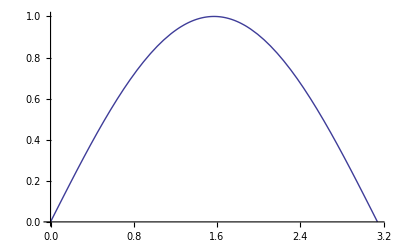

```mathematica
Plot[Sin[x], {x, 0, Pi}]
```

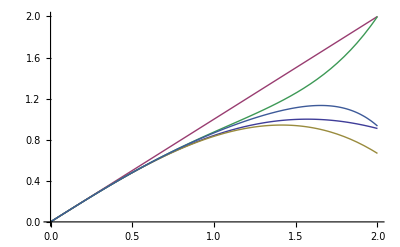

```mathematica
Plot[Tooltip[{Sin[x], x, x-x^3/6, x-x^3/6+x^5/24,  x-x^3/6+x^5/24-x^7/120}], {x, 0, 2}]
```

## Desarrollo de Taylor y Errores

```mathematica
(** Definitions **) f[x_]:=Sin[x];xp=5.0;n=35;sumaprevia=0;
```

```mathematica
Do[Subscript[sumapresente, i] = sumaprevia+(-1)^i*(xp)^(2*i+1)/((2 * i +1)!);
sumaprevia=Subscript[sumapresente, i], {i, 0, n}
];
Do[Subscript[errorverdadero, i]=f[xp]-Subscript[sumapresente, i];
Subscript[errorverdaderoabs, i]=Abs[f[xp]-Subscript[sumapresente, i]];
Subscript[errorverdaderorelativo, i]=(f[xp]-Subscript[sumapresente, i])/f[xp];
Subscript[errorverdaderorelativoporcentual, i]=Abs[(f[xp]-Subscript[sumapresente, i])/f[xp]*100];, {i, 0, n}
];
```

```mathematica
TableForm[Table[{i, f[xp],NumberForm[Subscript[sumapresente, i],{20, 20}], Subscript[errorverdadero, i], Subscript[errorverdaderoabs, i],Subscript[errorverdaderorelativo, i],Subscript[errorverdaderorelativoporcentual, i]},{i, 0, n}], TableHeadings->{None, {"i", "Valor Real", "Valor Aproximado", "E. Verdadero", "E.V. Absoluto", "E.V. Relativo", "E.V.R. Porcenrual"}}]
```

i | Valor Real | Valor Aproximado | E. Verdadero | E.V. Absoluto | E.V. Relativo | E.V.R. Porcenrual
0 | -0.958924 | 5.00000000000000000000 | -5.95892 | 5.95892 | 6.21418 | 621.418
1 | -0.958924 | -15.83333333333333000000 | 14.8744 | 14.8744 | -15.5116 | 1551.16
2 | -0.958924 | 10.20833333333333000000 | -11.1673 | 11.1673 | 11.6456 | 1164.56
3 | -0.958924 | -5.29265873015872800000 | 4.33373 | 4.33373 | -4.51937 | 451.937
4 | -0.958924 | 0.08963018077601690000 | -1.04855 | 1.04855 | 1.09347 | 109.347
5 | -0.958924 | -1.13361729898188000000 | 0.174693 | 0.174693 | -0.182176 | 18.2176
6 | -0.958924 | -0.93758404902067800000 | -0.0213402 | 0.0213402 | 0.0222543 | 2.22543
7 | -0.958924 | -0.96092134068272600000 | 0.00199707 | 0.00199707 | -0.00208261 | 0.208261
8 | -0.958924 | -0.95877636902261100000 | -0.000147906 | 0.000147906 | 0.000154241 | 0.0154241
9 | -0.958924 | -0.95893316519659600000 | 8.89053×10^-6 | 8.89053×10^-6 | -9.27136×10^-6 | 0.000927136
10 | -0.958924 | -0.95892383209100200000 | -4.42572×10^-7 | 4.42572×10^-7 | 4.6153×10^-7 | 0.000046153
11 | -0.958924 | -0.95892429321282000000 | 1.85497×10^-8 | 1.85497×10^-8 | -1.93443×10^-8 | 1.93443×10^-6
12 | -0.958924 | -0.95892427399941100000 | -6.63728×10^-10 | 6.63728×10^-10 | 6.92159×10^-10 | 6.92159×10^-8
13 | -0.958924 | -0.95892427468364900000 | 2.05106×10^-11 | 2.05106×10^-11 | -2.13892×10^-11 | 2.13892×10^-9
14 | -0.958924 | -0.95892427466258300000 | -5.55889×10^-13 | 5.55889×10^-13 | 5.797×10^-13 | 5.797×10^-11
15 | -0.958924 | -0.95892427466314900000 | 1.04361×10^-14 | 1.04361×10^-14 | -1.08831×10^-14 | 1.08831×10^-12
16 | -0.958924 | -0.95892427466313600000 | -2.9976×10^-15 | 2.9976×10^-15 | 3.12601×10^-15 | 3.12601×10^-13
17 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
18 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
19 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
20 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
21 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
22 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
23 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
24 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
25 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
26 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
27 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
28 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
29 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
30 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
31 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
32 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
33 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
34 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13
35 | -0.958924 | -0.95892427466313600000 | -2.66454×10^-15 | 2.66454×10^-15 | 2.77867×10^-15 | 2.77867×10^-13